# Projekt 2 - Normal Distribution

## KTH/ICT:IX1501 - Statistics

Joe Huldén, joeda@kth.se
Gustav Wiiala, wiiala@kth.se

KTH/ICT - Communication Systems

2015-12-03

## Det relativa felet av Normal Approximation

### Projekt 2 Situation: Antag att genomsnittet av 20 oberoende .s.v., normal fördelningen anses vara en god approximation. Hur som helst, i den här uppgiften kommer vi att gå bortom den rekommendationen och studera under vilken omständighet det är giltig. Exponential fördelningen är väldig skev jämförd med likformig fördelningen. Hur påverkar detta approximationen med normal fördelningen? I ett viss mobil system anländer nytt samtal med exponential fördelad ankomst tid med väntevärdet μ=λ^-1=3 minuter. Ankomst tiden är tiden mellan två samtal.

#### Sammanfattning

För att studera när det är möljigt och lämpligt att approximera så använder vi Gammafördelning, poisson fördelning och approximerar med normalfördelning. Därför att gammafördelningen och poisson fördelningen ger oss exakta fördelningar.

Uppgift 1

#### Diskussion med grafer som hjälpmedel

Uppgiften: Studera genomsnittet t̄=1/n ∑_(k=1)^n t_k av n=20 ankomst tider.
Vi plottar absolute error av pdf_(t̄)(t) och cdf_(t̄)(t) genom normal fördelningen för att studera hur absolute error förhåller sig till normal fördelningen. 
Vi har även gjort en plottning av relative error av gränsvärdena P(t̄>x), μ-2σ/√n<x<μ+2σ/√n

Graf 1.1: Exakt och Approximativt i pdf(t) där t är antalet minuter vi får vänta 

Vi förväntade oss i förväg få ett väntevärde på 60 då vi tittar på en summering av 20 stokastiska oberoende varibler där väntevärdet är 3minuter på varje. Den exakta- och approximativa fördelningen har relativt bra förhållning till varandra. Men det finns problem med att massan för den exakta gammadistrubtionen inte ligger lika symmetriskt kring sitt väntevärdet som normalfördelningen gör, vilket gör det svårare att approximera den här funktionen perfekt.

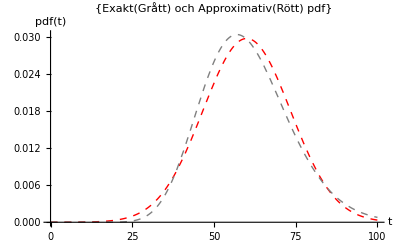

Graf 1.2: Exakt och Approximativt i cdf(t)  som ger oss sannolikheten att vi har väntat minst t minuter

Den exakta- och approximativa fördelningen har väldig bra förhållning till varandra. cdf är primitiva funktionen till pdf. Där t.ex. för att vänta i minst 60minuter är cdf(60). Man kan se att cdf funktionerna ser ut att stämma bättre överens än pdf funktionerna vilket verkar göra den till en okej approximation att använda.

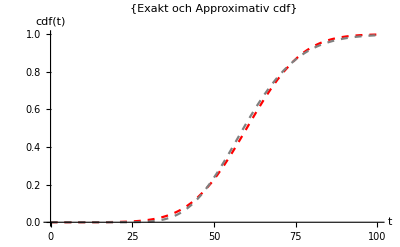

Graf 1.3: Absoluta Error bygger på formeln absoluteError(t) =  Pexact(t) - Papprox(t)

Grafen bygger på skillnaden mellan den approximativa- och den exakta- fördelningen. Då den exakta är mindre än den approximativa får vi en negativ absolute error.

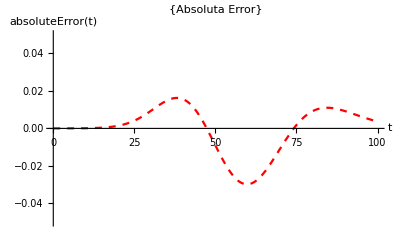

Graf 1.4: Relative Error bygger på formeln: RelativeError=absoluteError/exakt fördelning.
Grafen visar procentsatsen för relativa felet vid olika t.
Skillnaderna mellan de kumulativa funktionerna ökar markant då t>80 och det är då cdf:en för den exakta fördelningen som växer där.

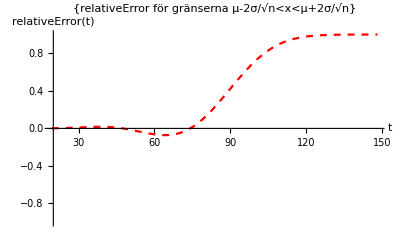

#### Kod som ska: Studera genomsnittet t̄=1/n ∑_(k=1)^n t_k av n=20 ankomst tider.

Uppgiften: Vi ritar upp graferna för absolute error av pdf_(t̄)(t) och cdf_(t̄)(t) för att studera hur det förhåller sig till normal fördelningen. 
Vi ritar även upp graferna för relative error med gränsvärden P(t̄>x), μ-2σ/√n<x<μ+2σ/√n

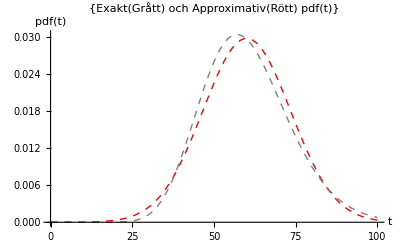

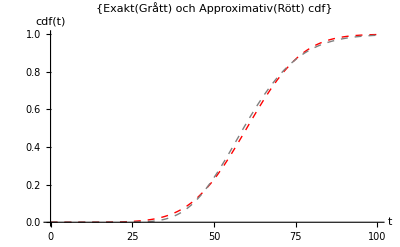

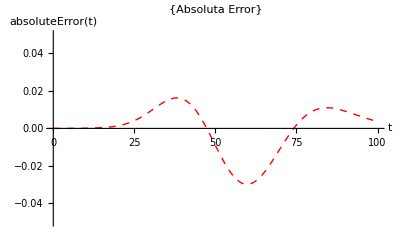

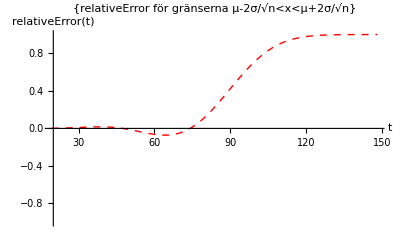

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
λ = 1/3; (* väntevärdet μ=λ^-1=3 *)
n = 20; (*antal iid rvs*)

gamma = GammaDistribution[n, 1/λ]; (*summa av exponential fördelad ankomst tid*)

Subscript[μ, exakt]  = Mean[gamma];(*medelvärdet*)

σ = StandardDeviation[gamma];


(*Approximativt*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ ];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[gamma,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;

relativeError[x_] := absoluteError[x]/Pexact[x];

(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
Plot[{PDF[approxi,t],PDF[gamma,t]},{t,0,100},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(Grått) och Approximativ(Rött) pdf(t)"},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->Full]

(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
Plot[{CDF[approxi,t],CDF[gamma,t]},{t,0,100},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(Grått) och Approximativ(Rött) cdf"},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}]

(*Plot av Absolut fel*)
Plot[{absoluteError[t]},{t,0,100},PlotRange -> {-0.05,.05},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[t],HoldForm[absoluteError[t]]}]

(*Plot av Relative Error*)
Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```

#### Slutsats

För små t så skiljer sig mätdata markant den exakta pdf/cdf och den normalapproximerad där den normalapproximerade antar betydligt större värden. Då ter det sig att ha så stor mätdata som möjligt. Det är naturligt att vi får bättre precision med större mätdata och intervall.

Uppgift 2

#### Diskussion med grafer som hjälpmedel

Uppgiften: Studera antalet av inkommande samtal under en timme.
Plottrar absolut och relativa error av sannolikhet funktionen genom normal approximationen.

Graf 2.1: Sannolikhet funktion antal samtal under 1h där n är antalet samtal och pdf(n) är sannolikheten n.
Vi kan se att det är störst sannolikhet att få exakt 20st samtal på en timme och den approximativa funktioner stämmer bra överens med den exakt Poissonfördelningen.

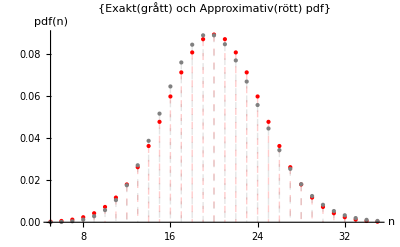

Graf 2.2: Täthetsfunktionen cdf(n) som säger hur sannolikheten att få minst eller lika många samtal n under en timme.

Man kan se att den approximativa täthetsfunktionen ger för låga sannolikheter för framförallt värdena 15<n< 28

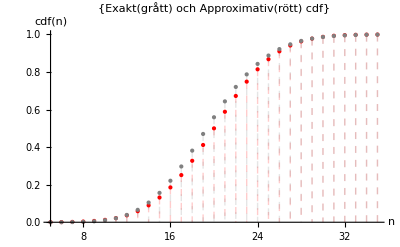

Graf 2.3: Absoluta Error antal samtal under 1h. 
Man ser tydligt här att det approximativa Normalfördelningen ger ett felvärde för 10<n<30 då negativa värden syns på y-axeln.

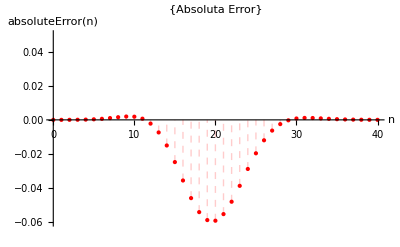

Graf 2.4: Relative Error bygger på formeln: RelativeError=absoluteError/exakt fördelning för antalet inkommand samtal under en timme.
Grafen visar procentsatsen för relativa felet vid olika t.

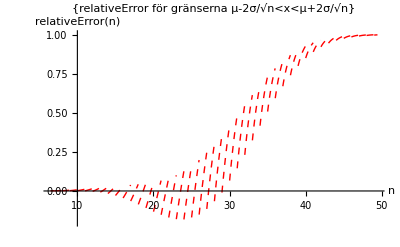

Graf 2.5 (Optional task): Sannolikhet funktion antal samtal under 5h där n är antalet samtal och pdf(n) är sannolikheten n.
Vi kan se att det är störst sannolikhet att få exakt 100st samtal på fem timmar och den approximativa funktioner stämmer väldigt exakt med Poissonfördelningen

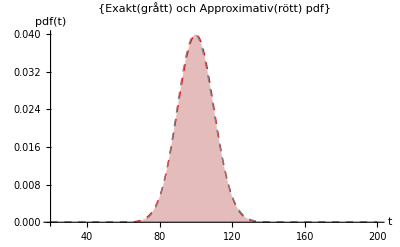

Graf 2.6 (Optional task): Täthetsfunktionen cdf(n) som säger hur sannolikheten att få minst eller lika många samtal n under fem timmar.

Man kan se att den approximativa täthetsfunktionen stämmer väldigt exakt för samtliga värden för t.

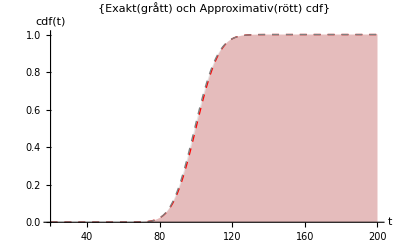

Graf 2.7 (Optional task): Absoluta Error antal samtal under 1h. 
Man ser tydligt här att det approximativa Normalfördelningen ger ett felvärde för 75<n<125 då negativa värden syns på y-axeln.

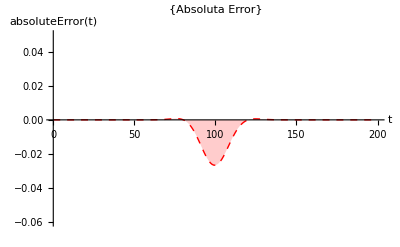

Graf 2.8 (Optional task): Relative Error bygger på formeln: RelativeError=absoluteError/exakt fördelning för antalet inkommand samtal under fem timmar.
Grafen visar procentsatsen för relativa felet vid olika t.

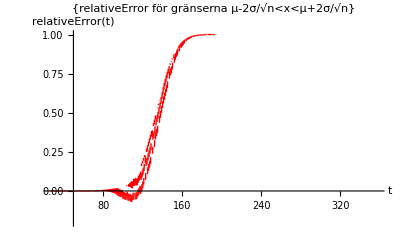

#### Kod som ska: Studera antalet inkommande samtal under en timme.

Uppgiften: Plotta absolute och relative error av sannolikhet funktionen genom normal approximationen.

-Graphics-

-Graphics-

-Graphics-

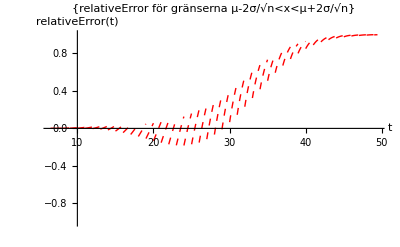

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
λ = 1/3; (*förväntade tidsintervall*)
n = 20; (*antalet iid rvs*)
T= 60;

(*exakta fördelningsfunktionen mottagna samtal under en timme *)
(*Inom tidsrymmen T är antalet händelser poissonfördelade*)
poisson = PoissonDistribution[λ *T];
Subscript[μ, exakt]  = Mean[poisson];
σ = StandardDeviation[poisson];

(*Approximativa disti*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ ];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[poisson,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;

relativeError[x_] := absoluteError[x]/Pexact[x]


(*Sannolikheten pf(n) = P("Exakt n samtal under en timme")*)
(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
DiscretePlot[{PDF[approxi,n],PDF[poisson,n]},{n,5,35},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(grått) och Approximativ(rött) pdf"},AxesLabel->{HoldForm[n],HoldForm[pdf[n]]}, PlotRange->Full]

(*Sannolikheten cdf(n) = P("Minst n samtal under en timme")*)
(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
DiscretePlot[{CDF[approxi,n],CDF[poisson,n]},{n,5,35},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(grått) och Approximativ(rött) cdf"},AxesLabel->{HoldForm[n],HoldForm[cdf[n]]}]


DiscretePlot[{absoluteError[n]},{n,0,40},PlotRange -> {-.06,.05},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[n],HoldForm[absoluteError[n]]}]

(*Plot av Relative Error*)


Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-1,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```

```mathematica
T= 60*5; (*hours intervall*)

(*exakta fördelningsfunktionen mottagna samtal under en timme *)
(*Inom tidsrymmen T är antalet händelser poissonfördelade*)
poisson = PoissonDistribution[λ *T];
Subscript[μ, exakt]  = Mean[poisson];
σ = StandardDeviation[poisson];

(*Approximativa disti*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ ];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[poisson,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;

relativeError[x_] := absoluteError[x]/Pexact[x]


(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
DiscretePlot[{PDF[approxi,t],PDF[poisson,t]},{t,20,200},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(grått) och Approximativ(rött) pdf"},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->Full]

(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
DiscretePlot[{CDF[approxi,t],CDF[poisson,t]},{t,20,200},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(grått) och Approximativ(rött) cdf"},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}]


DiscretePlot[{absoluteError[t]},{t,0,200},PlotRange -> {-.06,.05},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[t],HoldForm[absoluteError[t]]}]

(*Plot av Relative Error*)
Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-.2,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### Slutsats

För små t så skiljer sig mätdata markant den exakta pdf/cdf och den normalapproximerad där den normalapproximerade antar betydligt större värden. Då ter det sig att ha så stor mätdata som möjligt. Det är naturligt att vi får bättre precision med större mätdata och intervall.